```mathematica
Clear["Global`*"]
Needs["NumericalCalculus`"]
```

0.5

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

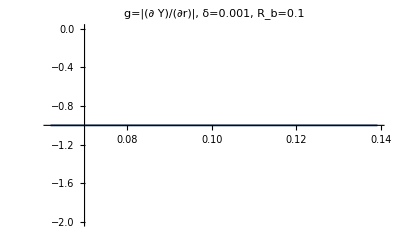

-0.2055

```mathematica
Ro=0.1;
Rmax = 2Ro;
sigma = 0.07197;
(*α = 1*10^(-5);
β = 10^3;*)
dim=2;
δ = 0.001;
jlev=13;
h1=0.5
γ=20;
(*δ = γ*h1/2^(jlev-1)*)
Y[r_,δ_]:=0.5(1-Tanh[(r-Ro)/(2*δ)]);
(*Yr2[r_, d_,,δ_]:=D[0.5(1-Tanh[(r1-Ro)/(2*d)]),r1]/.r1->r;*)
(*Yr[r_,δ_]:=D[Y[r1,δ],r1]/.r1-> r;*)
eps=0.001;
Yr[r_,δ_]:=(Y[r1+eps,δ] - Y[r1-eps,δ])/(2eps)/.r1-> r;
Yrr[r_,δ_]:=D[Y[r1,δ],{r1,2}]/.r1-> r;
g[r_,δ_]:=sigma*Yr[r,δ]*Sign[Yr[r,δ]];
gr[r_,δ_]:=sigma*Yrr[r,δ]*Sign[Yr[r,δ]];
(*g[r_]:=-sigma*Yr[r];
gr[r_]:=-sigma*Yrr[r];*)
ff[r_,δ_]:=-((dim-1)/r)*(gr[r,δ]+(dim-2)*gr[r,δ]/r);
ffreg[r_,δ_,floor_]:=-((dim-1)/(r+floor))*(gr[r,δ]+(dim-2)*gr[r,δ]/(r+floor));
title=", δ="<>ToString[δ]<>", R_b="<>ToString[Ro];
(*Manipulate[Plot[{Y[r,δ]},{r,0.001,Rmax}, GridLines->{Range[0,1,0.02],Range[0,1,0.2]}, PlotRange->All, PlotLabel->"Y[r]"<>title[δ]],{δ, 0.001, 0.05}]
Manipulate[Plot[{Y[r, γ*h1/2^(jlev-1)]},{r,0.001,Rmax}, GridLines->{Range[0,1,0.02],Range[0,1,0.2]}, PlotRange->All, PlotLabel->"Y[r]"<>title[δ]],{jlev, 7, 15}]
Manipulate[Plot[{g[r,δ]},{r,0.001,Rmax}, PlotRange->All, PlotLabel->"g=|(∂ Y)/(∂r)|"<>title[δ]],{δ, 0.005, 0.05}]

Manipulate[Plot[{gr[r,δ]},{r,0.001,Rmax}, PlotRange->All, PlotLabel->"(∂ g)/(∂r)"<>title[δ]],{δ, 0.005, 0.05}]
Manipulate[Plot[{ff[r,δ],ffreg[r,δ,floor]},{r,0.001,0.5Rmax}, PlotRange->All, PlotLabel->"∇·∇·Ω"<>title[δ]],{floor, 0.00000001, 1, 0.00001}]*)
(*Manipulate[Plot[{Yr2[r,d]},{r,0.001,Rmax}, PlotRange->All, PlotLabel->"(∂ Y)/(∂r)*δ"<>title],{d,0.001,0.1}]*)

Plot[{Yr[r,δ]/Abs[Yr[r,δ]]},{r,0.01,Rmax}, PlotRange->All, PlotLabel->"g=|(∂ Y)/(∂r)|"<>title]
Yr[1,1]
```

```mathematica
Manipulate[{Y[r],g[r],gr[r],ff[r],ffreg[r,0.1]},{r,0,Rmax, 0.0001}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

```mathematica
Plot3D[g[r]*(1-Cos[θ]^2),{r,0,1}]
```

```mathematica
D[Y[r],{r,3}]//Simplify
```

```mathematica
-(64. (-2.+1. Cosh[(8 (r-Ro))/δ]) Sech[(4 (r-Ro))/δ]^4)/δ^3
```

```mathematica
D[Yrr[r],{r}]
```

(64. Sech[(4 (r-Ro))/δ]^4)/δ^3-(128. Sech[(4 (r-Ro))/δ]^2 Tanh[(4 (r-Ro))/δ]^2)/δ^3

```mathematica
tang[x_,y_]:=(1/2)(1-Tanh[4(Sqrt[x^2+y^2]-Ro)/(δ)]);
dxtang[x_, y_]:=D[tang[Qx,y],{Qx,1}]/.Qx->x;
dytang[x_, y_]:=D[tang[x,Qy],{Qy,1}]/.Qy->y;
dY[x_,y_]:={dxtang[x, y], dytang[x, y]};
NdY[x_,y_]:=Sqrt[dxtang[x, y]^2+ dytang[x, y]^2];
(*regular[x_,y_]:=x/Sqrt[tmp[x,y]];*)

omega[x_,y_]:=NdY[x,y](IdentityMatrix[2]-(Transpose[{{x,y}}].{{x,y}})/tmp[x,y]);
f[xx_,yy_]:=(Div[Div[omega[x,y],{x,y}],{x,y}]/.x->xx/.y->yy);

(*Plot[{regular[dtang[δ*x]], tang[δ*x]},{x,-40,40},PlotRange->All]*)
(*Plot3D[{dxtang[x,y], dytang[x,y]},{x,-0.2,0.2},{y,-0.2,0.2},PlotRange->All]*)
(*Plot3D[{NdY[x,y]},{x,-0.2,0.2},{y,-0.2,0.2},PlotRange->All, PlotPoints->100]*)
(*Plot3D[{f[x,y]},{x,-0.2,0.2},{y,-0.2,0.2},PlotRange->{-1,1}, PlotPoints->100]*)
(*Plot3D[{omega[x,y][[1,1]],omega[x,y][[1,2]],omega[x,y][[2,1]],omega[x,y][[2,2]]},{x,-0.2,0.2},{y,-0.2,0.2},PlotRange->All, PlotPoints->20]*)
(*Plot3D[{Norm[omega[x,y]]},{x,-0.2,0.2},{y,-0.2,0.2},PlotRange->All, PlotPoints->100]*)
```

```mathematica
(*tangr[r_]:=(1/2)(1-Tanh[4(r-Ro)/(δ)]);
dY[r_]:=(D[tangr[r1],r1]/.r1->(rad[x,y]))*{x,y}/rad[x,y];
NdY[x_,y_]:=Sqrt[dY[x,y][[1]]^2+dY[x,y][[2]]^2];
normal[x_,y_]:=dY[x,y]/tmp[x,y];

Omegar[x_,y_]:=NdY[x,y]*(IdentityMatrix[2]- TensorProduct[normal[x,y],normal[x,y]]);
f[x_,y_]:=(Div[Div[Omegar[x1,y1],{x1,y1}],{x1,y1}])/.x1->x/.y1->y;
*)
```

```mathematica
myD[f_,var_]:=FullSimplify[D[TransformedField["Spherical"->"Cartesian",f,{r,θ,φ}->{x,y,z}],var]/.Thread[{x,y,z}->CoordinateTransformData["Spherical"->"Cartesian","Mapping",{r,θ,φ}]],Assumptions->r>0];

(*myD[f_,var_]:=FullSimplify[ND[     TransformedField["Spherical"->"Cartesian",f,{r,θ,φ}->{x,y,z}],var,]/.Thread[{x,y,z}->CoordinateTransformData["Spherical"->"Cartesian","Mapping",{r,θ,φ}]],Assumptions->r>0];*)
myGrad[f_]:={myD[f,x],myD[f,y],myD[f,z]};
myDiv[f_]:=myD[f[[1]],x]+myD[f[[2]],y]+myD[f[[3]],z];
myDivDiv[f_]:=Sum[myD[f[[i]][[1]],x]+myD[f[[i]][[2]],y]+myD[f[[i]][[3]],z], {i,1,3}];
```

```mathematica
(*

n[r1_,θ1_,φ1_]:= (gradtangr[r,θ,φ]/Sqrt[dtangr[r]^2+(α/δ)^2*Exp[-β*δ^2*(dtangr[r])^2]])/.r->r1/.θ->θ1/.φ->φ1;;*)

Omegar[r1_,θ1_,φ1_]:=(Sqrt[(dtangr[r])^2]*(Identity[3]-TensorProduct[n[r,θ,φ],n[r,θ,φ]]))/.r->r1/.θ->θ1/.φ->φ1;
f[r1_,θ1_,φ1_]:=myDivDiv[Omegar[r,θ,φ]]/.r->r1/.θ->θ1/.φ->φ1;

Clear["r", "θ","φ"]
R=0.05
θ1=0;
φ1=0;
Print["tangr[R]=",tangr[R]]
Print["dtangr[R]=",dtangr[R]]
Print["gradtangr[R]=",gradtangr[R,θ1,φ1 ]]
Print["n[R]=",n[R,θ1,φ1]]
Print["Omegar[R]=",Omegar[R,θ1,φ1]]
(*Print["f[R]=",f[R,θ1,φ1]]*)

(*Plot[{f[r1,θ1,φ1]},{r1,0.001,1}, PlotRange->{0,1}]*)
```

0.05

tangr[R]=0.982014

dtangr[R]=-1.41302

gradtangr[R]={0,0,0}

n[R]={0,0,0}

Omegar[R]={{4.23905,4.23905,4.23905},{4.23905,4.23905,4.23905},{4.23905,4.23905,4.23905}}

```mathematica
Plot[f[r1],{r1,0.001,1}]
```

$Aborted

```mathematica
f[0.05,0,0]
```

$Aborted

```mathematica
Sqrt[(dtangr[r])^2]*(Identity[3]-TensorProduct[n[r],n[r]])
```

$Aborted

```mathematica
ff[r_]:=(*{{r,0,0},{0,5r,0},{0,0,9r}}  *) {{r,2r,3r},{4r,5r,6r},{7r,8r,9r}}
```

```mathematica
ff[r][[1]][[2]]
```

2 r

```mathematica
myDivDiv[ff[r]]
```

18 Cos[θ]+12 Cos[φ] Sin[θ]+15 Sin[θ] Sin[φ]

```mathematica
Omegar[r,θ,φ]
myDivDiv[Omegar[r,θ,φ]]
```

{{3-(400 Cos[φ]^2 Sech[4-40 r]^4 Sin[θ]^2)/((ⅇ^(-4000000 Sech[40 (-1/10+r)]^4))/1000000000000+400 Sech[40 (-1/10+r)]^4),3-(400 Cos[φ] Sech[4-40 r]^4 Sin[θ]^2 Sin[φ])/((ⅇ^(-4000000 Sech[40 (-1/10+r)]^4))/1000000000000+400 Sech[40 (-1/10+r)]^4),3-(400 Cos[θ] Cos[φ] Sech[4-40 r]^4 Sin[θ])/((ⅇ^(-4000000 Sech[40 (-1/10+r)]^4))/1000000000000+400 Sech[40 (-1/10+r)]^4)},{3-(400 Cos[φ] Sech[4-40 r]^4 Sin[θ]^2 Sin[φ])/((ⅇ^(-4000000 Sech[40 (-1/10+r)]^4))/1000000000000+400 Sech[40 (-1/10+r)]^4),3-(400 Sech[4-40 r]^4 Sin[θ]^2 Sin[φ]^2)/((ⅇ^(-4000000 Sech[40 (-1/10+r)]^4))/1000000000000+400 Sech[40 (-1/10+r)]^4),3-(400 Cos[θ] Sech[4-40 r]^4 Sin[θ] Sin[φ])/((ⅇ^(-4000000 Sech[40 (-1/10+r)]^4))/1000000000000+400 Sech[40 (-1/10+r)]^4)},{3-(400 Cos[θ] Cos[φ] Sech[4-40 r]^4 Sin[θ])/((ⅇ^(-4000000 Sech[40 (-1/10+r)]^4))/1000000000000+400 Sech[40 (-1/10+r)]^4),3-(400 Cos[θ] Sech[4-40 r]^4 Sin[θ] Sin[φ])/((ⅇ^(-4000000 Sech[40 (-1/10+r)]^4))/1000000000000+400 Sech[40 (-1/10+r)]^4),3-(400 Cos[θ]^2 Sech[4-40 r]^4)/((ⅇ^(-4000000 Sech[40 (-1/10+r)]^4))/1000000000000+400 Sech[40 (-1/10+r)]^4)}}

$Aborted

```mathematica
myGrad[r]
```

{Cos[φ] Sin[θ],Sin[θ] Sin[φ],Cos[θ]}

```mathematica
FullSimplify[D[TransformedField["Spherical"->"Cartesian",r,{r,θ,φ}->{x,y,z}],x](*/.Thread[{x,y,z}->CoordinateTransformData["Spherical"->"Cartesian","Mapping",{r,θ,φ}]]*),Assumptions->r>0]
```

x/(√(x^2+y^2+z^2))

```mathematica
FullSimplify[D[(1-Tanh[4(r-Robj)/δ])/2,{r,3}]]
```

-(64 (-2+Cosh[(8 (r-Robj))/δ]) Sech[(4 (r-Robj))/δ]^4)/δ^3

```mathematica
FullSimplify[D[Sqrt[a^2+(α/δ)^2*Exp[-β*δ^2*(a)^2]],{a,2}]]
```

(ⅇ^(-a^2 β δ^2) α^2 (α^2 β (-1+a^2 β δ^2)+ⅇ^(a^2 β δ^2) (1+a^2 β δ^2+2 a^4 β^2 δ^4)))/(√(a^2+(ⅇ^(-a^2 β δ^2) α^2)/δ^2) (α^2+a^2 ⅇ^(a^2 β δ^2) δ^2))

```mathematica
D[Sqrt[a[r]^2+(α/δ)^2*Exp[-β*δ^2*(a[r])^2]],{r,2}]
```

-((2 a[r] a'[r]-2 ⅇ^(-β δ^2 a[r]^2) α^2 β a[r] a'[r])^2)/(4 ((ⅇ^(-β δ^2 a[r]^2) α^2)/δ^2+a[r]^2)^(3/2))+(2 a'[r]^2-2 ⅇ^(-β δ^2 a[r]^2) α^2 β a'[r]^2+4 ⅇ^(-β δ^2 a[r]^2) α^2 β^2 δ^2 a[r]^2 a'[r]^2+2 a[r] a''[r]-2 ⅇ^(-β δ^2 a[r]^2) α^2 β a[r] a''[r])/(2 √((ⅇ^(-β δ^2 a[r]^2) α^2)/δ^2+a[r]^2))

```mathematica
Simplify[D[a[r]/reg[r]/r,{r,2}]]
```

(r reg[r] (-2 r a'[r] reg'[r]+reg[r] (-2 a'[r]+r a''[r]))+a[r] (2 reg[r]^2+2 r^2 reg'[r]^2+r reg[r] (2 reg'[r]-r reg''[r])))/(r^3 reg[r]^3)

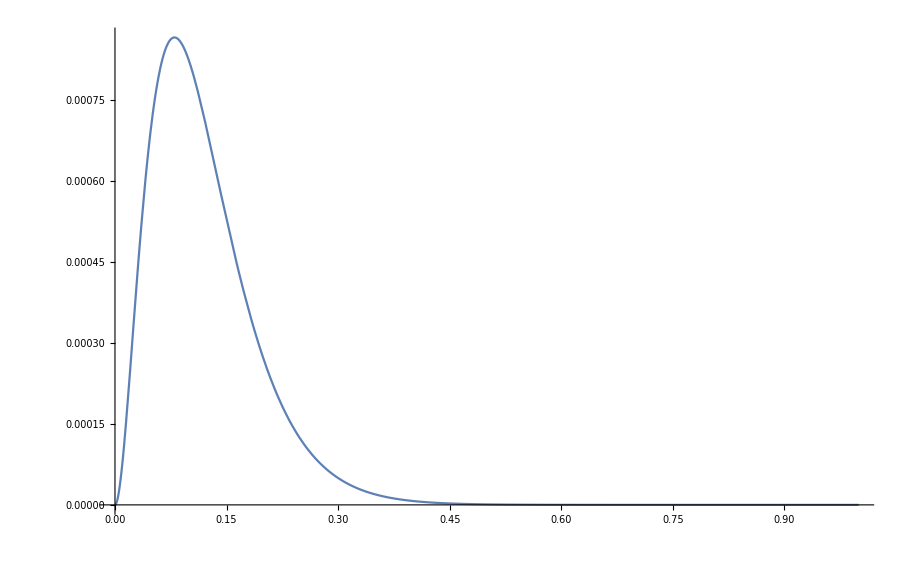

```mathematica
Plot[x^2*Exp[-(25*x)],{x,0,1}]
```

```mathematica
D[x^2*Exp[-(25*x)],{x,2}]
```

2 ⅇ^(-25 x)-100 ⅇ^(-25 x) x+625 ⅇ^(-25 x) x^2

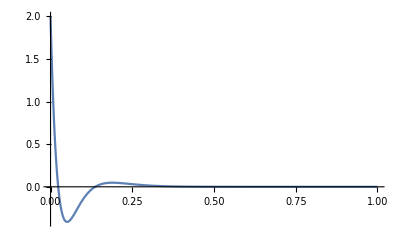

```mathematica
Plot[2 ⅇ^(-25 x)-100 ⅇ^(-25 x) x+625 ⅇ^(-25 x) x^2,{x,0,1}, PlotRange->All]
```

```mathematica
(*fex[x_]:=(-Exp[-(x-0.1)^2*10000]+Exp[-(x-0.15)^2*10000]-Exp[-(x+0.1)^2*10000]+Exp[-(x+0.15)^2*10000])*10000;*)
fex[x_]:=-gr[x];
s=DSolve[{x*u''[x]+u'[x]==fex[x], u[-1]==1, u[1]==1},u,x]
(*s=DSolve[{u''[x]==fex[x], u[-1]==1, u[1]==1},u,x]*)
Plot[{u[x]/.s[[1]](*,fex[x]*)},{x,0-1,1}, PlotRange->All]
```

{{u→Function[{x},(10 π-π x^3+2 ⅈ Log[x])/(9 π)]}}

-Graphics-

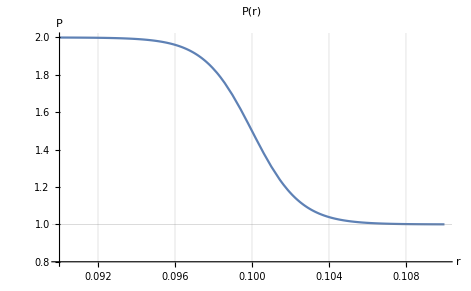

```mathematica
Plot[{1+Y[r]},{r,0.09,0.11}, GridLines->{Range[0,1,0.02],Range[0,1,0.2]}, PlotRange->{0.8,2}, PlotLabel->"P(r)", AxesLabel->{Style[r,Large,Bold,Blue],Style[P,Large,Bold,Blue]}]
```

```mathematica
1+Log2[20*0.5/0.006]
```

11.7027

```mathematica
ToString[title]<>"qw"
```

, δ=0.00244141, R =0.1
                 bqw